```mathematica
(* Available Plays *)
plays={"Midsummer Night's Dream", "Romeo and Juliet","Hamlet","King Lear", "Antigone"};
```

```mathematica
(* Process Plays *)
(*sceneNumbers={"1.1","1.2","2.1","2.2","3.1","3.2","4.1","4.2","5.1"};*)
sceneNumbers={"1.0","1.1","1.2","1.3","1.4","1.5","2.0","2.1","2.2","2.3","2.4","2.5","2.6","3.1","3.2","3.3","3.4","3.5","4.1","4.2","4.3","4.4","4.5","5.1","5.2","5.3"};

files=FileNames["*.txt",NotebookDirectory[]]
Import[#]&/@files⟦;;⟧
SetDirectory[NotebookDirectory[]];
(*Map[
Export["Midsummer_scene_"<>ToString[#]<>".txt",Import["http://shakespeare.mit.edu/midsummer/midsummer."<>ToString[#]<>".html","Source"],"Text"]&,sceneNumbers];*)
Export["Plays_Of_Sophocles",Import["https://www.gutenberg.org/files/31/31-h/31-h.htm.html","Source"],"Text"]

sceneFiles="Midsummer_scene_"<>#<>".txt"&/@sceneNumbers;
text=StringJoin[Import/@sceneFiles];
speakerOrder=Map[StringCases[Import["Midsummer_scene_"<>ToString[#]<>".txt"],Shortest["<b>"~~x__~~"</b>"]->x]&,sceneNumbers]//Flatten;
(* For MSND, Fix "HERNIA" typos *)
speakerOrder=speakerOrder/."HERNIA"->"HERMIA";
nameList=DeleteCases[Union@Flatten@speakerOrder,"HERNIA"];
```

{C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_1.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_1.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_1.3.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_1.4.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_1.5.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_2.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_2.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_3.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_3.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_3.3.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_3.4.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_4.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_4.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_4.3.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_4.4.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_4.5.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_4.6.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_4.7.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_5.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Hamlet_scene_5.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_1.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_1.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_1.3.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_1.4.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_1.5.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_2.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_2.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_2.3.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_2.4.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_3.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_3.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_3.3.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_3.4.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_3.5.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_3.6.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_3.7.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_4.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_4.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_4.3.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_4.4.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_4.5.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_4.6.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_4.7.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_5.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_5.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Lear_scene_5.3.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Midsummer_scene_1.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Midsummer_scene_1.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Midsummer_scene_2.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Midsummer_scene_2.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Midsummer_scene_3.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Midsummer_scene_3.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Midsummer_scene_4.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Midsummer_scene_4.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Midsummer_scene_5.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_1.0.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_1.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_1.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_1.3.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_1.4.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_1.5.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_2.0.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_2.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_2.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_2.3.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_2.4.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_2.5.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_2.6.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_3.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_3.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_3.3.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_3.4.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_3.5.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_4.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_4.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_4.3.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_4.4.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_4.5.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_5.1.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_5.2.txt,C:\Users\jason\OneDrive\Desktop\Documents\Relationship Project\Romeo_Juliet_scene_5.3.txt}

{<!DOCTYPE HTML PUBLIC "-//W3C//DTD HTML 4.0 Transitional//EN"
 "http://www.w3.org/TR/REC-html40/loose.dtd">
 <html>
 <head>
 <title>SCENE I. Elsinore. A platform before the castle.
 </title>
 <meta http-equiv="Content-Type" content="text/html; charset=iso-8859-1">
 <LINK rel="stylesheet" typ…blockquote>
<table width="100%" bgcolor="#CCF6F6">
<tr><td class="nav" align="center">
      <a href="/Shakespeare">Shakespeare homepage</A> 
    | <A href="/Shakespeare/hamlet/">Hamlet</A> 
    | Act 1, Scene 1
   <br>
      <a href="hamlet.1.2.html">Next scene</A>
</table>

</body>
</html>
,79,…}
 |  |  |  |

Import::nffil: File Midsummer_scene_1.0.txt not found during Import.

Import::nffil: File Midsummer_scene_1.3.txt not found during Import.

Import::nffil: File Midsummer_scene_1.4.txt not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in «1».

StringJoin::string: String expected at position 3 in «1».

StringJoin::string: String expected at position 4 in «1».

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Import::nffil: File Midsummer_scene_1.0.txt not found during Import.

StringCases::strse: String or list of strings expected at position 1 in StringCases[$Failed,Shortest[<b>~~x__~~</b>]→x].

Import::nffil: File Midsummer_scene_1.3.txt not found during Import.

StringCases::strse: String or list of strings expected at position 1 in StringCases[$Failed,Shortest[<b>~~x__~~</b>]→x].

Import::nffil: File Midsummer_scene_1.4.txt not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

StringCases::strse: String or list of strings expected at position 1 in StringCases[$Failed,Shortest[<b>~~x__~~</b>]→x].

General::stop: Further output of StringCases::strse will be suppressed during this calculation.

```mathematica
(* Separates lines of text ready for sentiment analysis *)
lines=StringSplit[text,Shortest["<b>"~~x__~~"</b>"]];
lines=StringDelete[lines,Shortest["<"~~x___~~">"]]//Rest;
lines=StringDelete[lines,Shortest["Shakespeare homepage"~~x__~~"Enter"]];
sentences=lines//TextSentences;
lineLength=Length/@sentences;
```

```mathematica
(* Create directed edges for graph *)
speakerBySentence=Table[Table[speakerOrder⟦i⟧,Length[sentences⟦i⟧]],{i,1,Length[lines]}]//Flatten;
recipientByLine=Table[Table[speakerOrder⟦i-1⟧,Length[sentences⟦i⟧]],{i,2,Length[lines]}];
recipientByLine=Prepend[recipientByLine,Table[speakerOrder⟦2⟧,Length[First[sentences]]]];
recipientBySentence=Table[Table[speakerOrder⟦i-1⟧,Length[sentences⟦i⟧]],{i,2,Length[lines]}]//Flatten;
recipientBySentence=Nest[Prepend[speakerOrder⟦2⟧],recipientBySentence,Length[First[sentences]]];

emphasis=WordFrequency[Flatten[sentences],#,IgnoreCase->True]&/@nameList;
diffRecipientPos=Position[emphasis,_?Positive];
diffRecipientPos=SortBy[diffRecipientPos,Last];
diffRecipient=First/@diffRecipientPos;
diffSentence=Last/@diffRecipientPos;

brokenInd=TakeList[Range[Length[recipientBySentence]],lineLength];
sentenceToLineRules=Table[i->First@@Position[brokenInd,i],{i,1,Length[recipientBySentence]}];
lineIndOfSentences=Range[Length[recipientBySentence]]/.sentenceToLineRules;
sentenceNumOfDiffLine[x_]:=Last@diffRecipientPos⟦x⟧-Total[lineLength⟦;;lineIndOfSentences⟦Last@diffRecipientPos⟦x⟧⟧-1⟧];

For[i=1,i≤Length[diffRecipientPos],i++,
recipientByLine⟦lineIndOfSentences⟦Last@diffRecipientPos⟦i⟧⟧,sentenceNumOfDiffLine[i];;⟧=nameList⟦First@diffRecipientPos⟦i⟧⟧]

recipientBySentence=recipientByLine//Flatten;
finalRules=Table[speakerBySentence⟦i⟧->recipientBySentence⟦i⟧,{i,1,Length[speakerBySentence]}];
rules=DeleteCases[DeleteDuplicates[finalRules],x_->x_];
rules=rules/."HERNIA"->"HERMIA";
```

```mathematica
(* Implement Sentiment Analysis of lines *)
feelings=Classify["Sentiment",#,"Probabilities"]&/@sentences//Flatten;
```

```mathematica
(* Put sentiment into edges *)
{pos,neu,neg}=Table[feelings⟦i⟧[#],{i,1,Length[feelings]}]&/@{"Positive","Neutral","Negative"};
Health=(pos-neg)/(1+neu);
sentenceHealth={finalRules⟦#⟧,Health⟦#⟧}&/@Range[Length[Health]];
sentenceHealthFormat=Cases[sentenceHealth,{#,_}]&/@rules;
relationshipHealth=Table[Mean[Table[sentenceHealthFormat⟦i⟧⟦j⟧⟦2⟧,{j,1,Length[sentenceHealthFormat⟦i⟧]}]],{i,1,Length[sentenceHealthFormat]}];
```

```mathematica
(* Incorporate Frequency for into Health *)
freq=Table[Length[sentenceHealthFormat⟦i⟧],{i,1,Length[sentenceHealthFormat]}];
freqMultiplier[x_]:=(Log[x]+3)/3;
thickness=N[freq]/Max[N[freq]]*.012;
edgeWidth=Table[rules⟦i⟧->freqMultiplier[N[freq⟦i⟧]],{i,Length[rules]}];
```

```mathematica
(* Exclude Neutral/Conflicted Relationships *)
relationshipHealthFinal=relationshipHealth*N[freqMultiplier[freq]];
viableEdges=Position[relationshipHealthFinal,x_/;x>.20||x<-.20]//Flatten;
relationshipHealthFinalExc=Table[relationshipHealthFinal⟦i⟧,{i,viableEdges}];
viableFreq=Table[freq⟦i⟧,{i,viableEdges}];
viableThickness=Table[thickness⟦i⟧,{i,viableEdges}];
viableEdgeWidth=Table[edgeWidth⟦i⟧,{i,viableEdges}];
```

```mathematica
(* Modify the Graph with color (health) and width (frequency) *)
relationshipColors=Table[Blend[{Red,Green},(i+1)/2],{i,relationshipHealthFinalExc}]
```

{RGBColor[0.333918909189551, 0.666081090810449, 0.],RGBColor[0.386235352697487, 0.613764647302513, 0.],RGBColor[0.27291971289903527, 0.7270802871009647, 0.],RGBColor[0.11195074664124949, 0.8880492533587505, 0.],RGBColor[0.1925083312963023, 0.8074916687036977, 0.],RGBColor[0.3546615100233971, 0.6453384899766029, 0.],RGBColor[0.140727635037312, 0.859272364962688, 0.],RGBColor[0.3708092980362676, 0.6291907019637324, 0.],RGBColor[0.3823046677144064, 0.6176953322855936, 0.],RGBColor[0.2879770526860239, 0.7120229473139761, 0.],RGBColor[0.34745957511914427, 0.6525404248808557, 0.],RGBColor[0.19019531289119707, 0.8098046871088029, 0.],RGBColor[0.34828824958919424, 0.6517117504108058, 0.],RGBColor[0.26310389336636175, 0.7368961066336382, 0.],RGBColor[0.604883146159694, 0.395116853840306, 0.],RGBColor[0.3424786087161962, 0.6575213912838038, 0.],RGBColor[0.30439817596428287, 0.6956018240357171, 0.],RGBColor[0.36776625749896774, 0.6322337425010323, 0.],RGBColor[0.6501240069511719, 0.3498759930488281, 0.],RGBColor[0.7158564759050839, 0.28414352409491606, 0.],RGBColor[0.3647392202510895, 0.6352607797489105, 0.],RGBColor[0.3066785649614341, 0.6933214350385659, 0.],RGBColor[0.10740208304937504, 0.892597916950625, 0.],RGBColor[0.39886183801152997, 0.60113816198847, 0.],RGBColor[0.6223649479465552, 0.3776350520534449, 0.],RGBColor[0.3545443760104572, 0.6454556239895428, 0.],RGBColor[0.3665280934222329, 0.6334719065777671, 0.],RGBColor[0.37651452657519424, 0.6234854734248058, 0.],RGBColor[0.39285673871208293, 0.6071432612879171, 0.],RGBColor[0.2313561171713192, 0.7686438828286808, 0.],RGBColor[0.38768905676392473, 0.6123109432360753, 0.],RGBColor[0.38117891038146545, 0.6188210896185345, 0.],RGBColor[0.14051043943525476, 0.8594895605647452, 0.],RGBColor[0.34229094640446744, 0.6577090535955326, 0.],RGBColor[0.33037458012293164, 0.6696254198770684, 0.],RGBColor[0.3096928412171953, 0.6903071587828047, 0.],RGBColor[0.26241345741927713, 0.7375865425807229, 0.],RGBColor[0.3805286630784228, 0.6194713369215772, 0.],RGBColor[0.1711482743646242, 0.8288517256353758, 0.],RGBColor[0.2709959298913144, 0.7290040701086856, 0.],RGBColor[0.28441564811847975, 0.7155843518815203, 0.],RGBColor[0.27596449431421577, 0.7240355056857842, 0.],RGBColor[0.2707599256028065, 0.7292400743971935, 0.],RGBColor[0.3201031029465148, 0.6798968970534852, 0.],RGBColor[0.2807244695929264, 0.7192755304070736, 0.],RGBColor[0.38230114391260517, 0.6176988560873948, 0.],RGBColor[0.13421067408891352, 0.8657893259110865, 0.],RGBColor[0.36925096442932404, 0.630749035570676, 0.],RGBColor[0.29544474632560513, 0.7045552536743949, 0.],RGBColor[0.21341566581518512, 0.7865843341848149, 0.],RGBColor[0.7158564759050839, 0.28414352409491606, 0.],RGBColor[0.39880129766237904, 0.601198702337621, 0.],RGBColor[0.3508095087412989, 0.6491904912587011, 0.],RGBColor[0.6151672332616565, 0.3848327667383436, 0.],RGBColor[0.7720144824578195, 0.2279855175421805, 0.],RGBColor[0.3990156845755978, 0.6009843154244022, 0.],RGBColor[0.30984018488385956, 0.6901598151161404, 0.],RGBColor[0.3644713739222747, 0.6355286260777253, 0.],RGBColor[0.9023641962038702, 0.0976358037961298, 0.],RGBColor[0.39310635514325065, 0.6068936448567493, 0.],RGBColor[0.3023497674700384, 0.6976502325299616, 0.],RGBColor[0.3175324920032295, 0.6824675079967705, 0.],RGBColor[0.3159312948248233, 0.6840687051751767, 0.],RGBColor[0.6854366929949394, 0.31456330700506063, 0.],RGBColor[0.2875104735036563, 0.7124895264963437, 0.],RGBColor[0.16859421966228716, 0.8314057803377128, 0.],RGBColor[0.030679981269169376, 0.9693200187308306, 0.],RGBColor[0.15554202010888685, 0.8444579798911132, 0.],RGBColor[0.24759463989143482, 0.7524053601085652, 0.],RGBColor[0.24759463989143482, 0.7524053601085652, 0.],RGBColor[0.24759463989143482, 0.7524053601085652, 0.],RGBColor[0.27856280602986583, 0.7214371939701342, 0.],RGBColor[0.2580766833205719, 0.7419233166794281, 0.],RGBColor[0.35826388621133376, 0.6417361137886662, 0.],RGBColor[0.277134055981636, 0.722865944018364, 0.],RGBColor[0.358782928578934, 0.641217071421066, 0.],RGBColor[0.14643664672532575, 0.8535633532746743, 0.],RGBColor[0.3059174460727735, 0.6940825539272265, 0.],RGBColor[0.3853220019207705, 0.6146779980792295, 0.],RGBColor[0.3042779860523336, 0.6957220139476664, 0.],RGBColor[0.2709159195210926, 0.7290840804789074, 0.],RGBColor[0.2709159195210926, 0.7290840804789074, 0.],RGBColor[0.34044209846334983, 0.6595579015366502, 0.],RGBColor[0.07966708764130259, 0.9203329123586974, 0.],RGBColor[0.31452073521589596, 0.685479264784104, 0.],RGBColor[0.2340547120352019, 0.7659452879647981, 0.],RGBColor[0.7427724371717999, 0.25722756282820014, 0.],RGBColor[0.6121312874078821, 0.38786871259211786, 0.],RGBColor[0.3616446157401243, 0.6383553842598757, 0.],RGBColor[0.2932611331432702, 0.7067388668567298, 0.],RGBColor[0.1278647026618287, 0.8721352973381713, 0.],RGBColor[0.6354298913610424, 0.36457010863895756, 0.],RGBColor[0.22668576196767276, 0.7733142380323272, 0.],RGBColor[0.6679500629140951, 0.33204993708590486, 0.],RGBColor[0.35588204632536724, 0.6441179536746328, 0.],RGBColor[0.3428766008498978, 0.6571233991501022, 0.],RGBColor[0.9744169704888117, 0.025583029511188238, 0.],RGBColor[0.6685448797989244, 0.3314551202010756, 0.],RGBColor[0.6434257534255375, 0.35657424657446246, 0.],RGBColor[0.15811061751610445, 0.8418893824838956, 0.],RGBColor[0.38422257538905424, 0.6157774246109458, 0.],RGBColor[0.23510052514296764, 0.7648994748570324, 0.],RGBColor[0., 1., 0.],RGBColor[0.18954394229511062, 0.8104560577048894, 0.],RGBColor[0.3888202529475693, 0.6111797470524307, 0.],RGBColor[0.3875618509635963, 0.6124381490364037, 0.],RGBColor[0.7639013256763277, 0.23609867432367226, 0.],RGBColor[0.3528443905860561, 0.6471556094139439, 0.],RGBColor[0.35630145227787813, 0.6436985477221219, 0.],RGBColor[0., 1., 0.],RGBColor[0.6292795915578671, 0.37072040844213294, 0.],RGBColor[0.7152142090282276, 0.28478579097177237, 0.],RGBColor[0.3507652740851408, 0.6492347259148592, 0.],RGBColor[0.9742257946548991, 0.025774205345100887, 0.],RGBColor[0.32496794227761217, 0.6750320577223878, 0.],RGBColor[0.37087541521896283, 0.6291245847810372, 0.]}

```mathematica
viableRules=Table[rules⟦i⟧,{i,viableEdges}];
edgeColors=Table[viableRules⟦i⟧->relationshipColors⟦i⟧,{i,Length[viableRules]}];
```

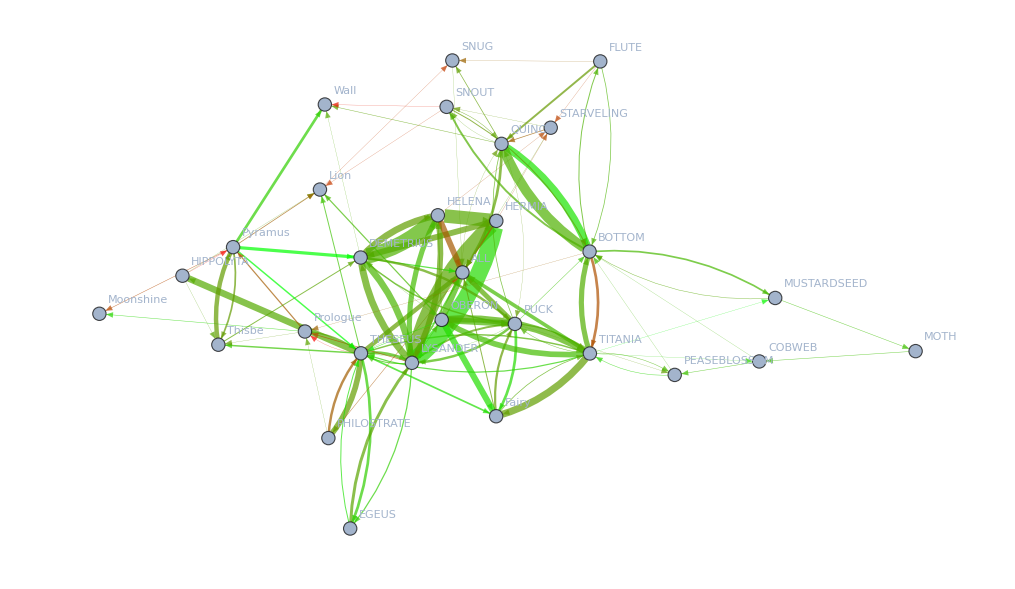

```mathematica
edgeThickness=Thread[viableRules->(Thickness[#]&/@viableThickness)];
edgeFormat=Table[viableRules⟦i⟧->Directive[Values[edgeThickness]⟦i⟧,Values[edgeColors]⟦i⟧],{i,1,Length[edgeColors]}];
g=Graph[viableRules,VertexLabels->All,EdgeStyle->edgeFormat]
```

```mathematica
CommunityGraphPlot[g]
```

-Graphics-